# Tutorial notebook

CmdStan package

```mathematica
<<CmdStan`
```

```mathematica
?CmdStan`*
```

## Linear regression

Stan code

```mathematica
SetDirectory[$TemporaryDirectory]
```

/tmp

```mathematica
stanCode="data
{
  int<lower = 0> N;
  vector[N] x;
  vector[N] y;
}
parameters
{
  real alpha;
  real beta;
  real<lower = 0> sigma;
}
model {
  y ~normal(alpha + beta * x, sigma);
}";
```

```mathematica
stanCodeFile=ExportStanCode["linear_regression.stan",stanCode]
```

/tmp/linear_regression.stan

Stan exe

```mathematica
stanExeFile = CompileStanCode[stanCodeFile,StanVerbose->False]
```

/tmp/linear_regression

Linear regression data

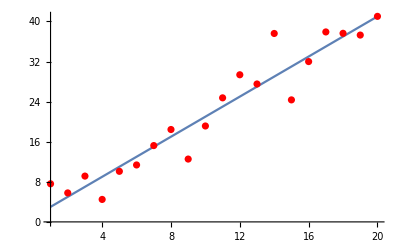

```mathematica
σ=3;α=1;β=2;
n=20;
X=Range[n];
Y=α+β*X+RandomVariate[NormalDistribution[0,σ],n];
Show[Plot[α+β*x,{x,Min[X],Max[X]}],ListPlot[Transpose@{X,Y},PlotStyle->Red]]
```

```mathematica
Export["~/GitHub/MathematicaStan/figures/linRegData.png",%]
```

~/GitHub/MathematicaStan/figures/linRegData.png

Stan data.R file

```mathematica
stanData=<|"N"->n,"x"->X,"y"->Y|>;
stanDataFile=ExportStanData[stanExeFile,stanData]
```

/tmp/linear_regression.data.R

Run Stan: “method=Optimize”

```mathematica
stanResultFile=RunStan[stanExeFile,OptimizeDefaultOptions]
```

Running: /tmp/linear_regression method=optimize data file=/tmp/linear_regression.data.R output file=/tmp/linear_regression.csv

method = optimize
  optimize
    algorithm = lbfgs (Default)
      lbfgs
        init_alpha = 0.001 (Default)
        tol_obj = 9.9999999999999998e-13 (Default)
        tol_rel_obj = 10000 (Default)
        tol_grad = 1e-08 (Default)
        tol_rel_grad = 10000000 (Default)
        tol_param = 1e-08 (Default)
        history_size = 5 (Default)
    iter = 2000 (Default)
    save_iterations = 0 (Default)
id = 0 (Default)
data
  file = /tmp/linear_regression.data.R
init = 2 (Default)
random
  seed = 3036422700
output
  file = /tmp/linear_regression.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)

Initial log joint probability = -6230.82
    Iter      log prob        ||dx||      ||grad||       alpha      alpha0  # evals  Notes 
Error evaluating model log probability: Non-finite gradient.
Error evaluating model log probability: Non-finite gradient.

      20      -35.2776    0.00157027   0.000475905      0.9838      0.9838       52   
Optimization terminated normally: 
  Convergence detected: relative gradient magnitude is below tolerance

/tmp/linear_regression.csv

```mathematica
RunStan[stanExeFile,OptimizeDefaultOptions,StanVerbose->False]
```

/tmp/linear_regression.csv

```mathematica
OptimizeDefaultOptions
```

method=optimize

Load result

```mathematica
stanResult=ImportStanResult[stanResultFile]
```

file: /tmp/linear_regression.csv
     meta: lp__ 
parameter: alpha , beta , sigma

```mathematica
GetStanResultMeta[stanResult,"lp__"]
αe=GetStanResult[stanResult,"alpha"]
βe=GetStanResult[stanResult,"beta"]
σe=GetStanResult[stanResult,"sigma"]
```

{-35.2776}

{1.25552}

{1.99124}

{3.53913}

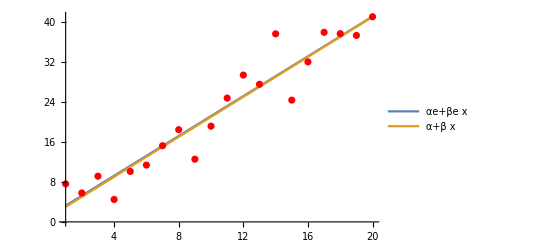

~/GitHub/MathematicaStan/figures/linRegEstimate.png

```mathematica
Show[Plot[{αe+βe*x,α+β*x},{x,Min[X],Max[X]},PlotLegends->"Expressions"],ListPlot[Transpose@{X,Y},PlotStyle->Red]]
Export["~/GitHub/MathematicaStan/figures/linRegEstimate.png",%]
```

Run Stan: “method=Variational”

```mathematica
myOpt=VariationalDefaultOptions
```

method=variational

```mathematica
myOpt=SetStanOption[myOpt,"output.file",FileNameJoin[{Directory[],"myOutputFile.csv"}]]
```

method=variational output file=/tmp/myOutputFile.csv

```mathematica
myOpt=SetStanOption[myOpt,"method.adapt.iter",123]
```

method=variational adapt iter=123 output file=/tmp/myOutputFile.csv

```mathematica
GetStanOption[myOpt,"method.adapt.iter"]
```

123

```mathematica
myOpt=RemoveStanOption[myOpt,"method.adapt.iter"]
```

method=variational output file=/tmp/myOutputFile.csv

```mathematica
myOutputFile=RunStan[stanExeFile,myOpt,StanVerbose->False]
```

/tmp/myOutputFile.csv

```mathematica
myResult=ImportStanResult[myOutputFile]
```

file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma

1.35524

0.869578

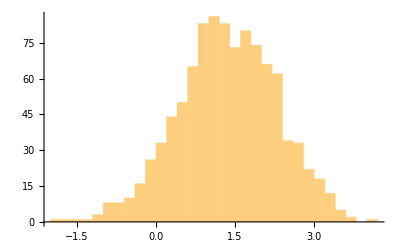

```mathematica
GetStanResult[Mean,myResult,"alpha"]
GetStanResult[Variance,myResult,"alpha"]
GetStanResult[Histogram,myResult,"alpha"]
```

## Linear regression, more than one predictor

Stan code

```mathematica
stanCode="data {
  int<lower=0> N;   // number of data items
  int<lower=0> K;   // number of predictors
  matrix[N, K] x;   // predictor matrix
  vector[N] y;      // outcome vector
}
parameters {
  real alpha;           // intercept
  vector[K] beta;       // coefficients for predictors
  real<lower=0> sigma;  // error scale
}
model {
  y ~ normal(x * beta + alpha, sigma);  // likelihood
}";
```

```mathematica
stanCodeFile=ExportStanCode["linear_regression_vect.stan",stanCode];
stanExeFile = CompileStanCode[stanCodeFile,StanVerbose->False];
```

Generate data

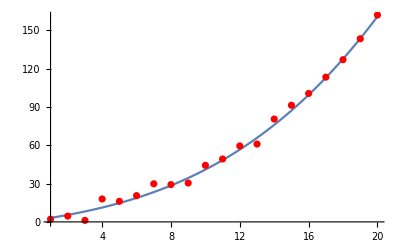

```mathematica
σ=3;α=1;β1=2;β2=0.1;β3=0.01;
n=20;
X=Range[n];
Y=α+β1*X+β2*X^2+β3*X^3+RandomVariate[NormalDistribution[0,σ],n];
Show[Plot[α+β1*x+β2*x^2+β3*x^3,{x,Min[X],Max[X]}],ListPlot[Transpose@{X,Y},PlotStyle->Red]]
```

```mathematica
Export["~/GitHub/MathematicaStan/figures/linReg2Data.png",%]
```

~/GitHub/MathematicaStan/figures/linReg2Data.png

Export data

```mathematica
stanData=<|"N"->n,"K"->3,"x"->Transpose[{X,X^2,X^3}],"y"->Y|>;
stanDataFile=ExportStanData[stanExeFile,stanData]
```

/tmp/linear_regression_vect.data.R

Run Stan: “method=Sample”

```mathematica
stanResultFile=RunStan[stanExeFile,SampleDefaultOptions]
```

Running: /tmp/linear_regression_vect method=sample data file=/tmp/linear_regression_vect.data.R output file=/tmp/linear_regression_vect.csv

method = sample (Default)
  sample
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
      delta = 0.80000000000000004 (Default)
      kappa = 0.75 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)
        metric = diag_e (Default)
        metric_file =  (Default)
        stepsize = 1 (Default)
        stepsize_jitter = 0 (Default)
id = 0 (Default)
data
  file = /tmp/linear_regression_vect.data.R
init = 2 (Default)
random
  seed = 3043713420
output
  file = /tmp/linear_regression_vect.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)


Gradient evaluation took 4e-05 seconds
1000 transitions using 10 leapfrog steps per transition would take 0.4 seconds.
Adjust your expectations accordingly!


Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 0.740037 seconds (Warm-up)
               0.60785 seconds (Sampling)
               1.34789 seconds (Total)

/tmp/linear_regression_vect.csv

Load the CSV file

```mathematica
stanResult=ImportStanResult[stanResultFile]
```

file: /tmp/linear_regression_vect.csv
     meta: lp__ , accept_stat__ , stepsize__ , treedepth__ , n_leapfrog__ , divergent__ , energy__ 
parameter: alpha , beta 3, sigma

```mathematica
{β1e,β2e,β3e}=GetStanResult[Mean,stanResult,"beta"]
```

{3.30321,-0.010088,0.0126913}

```mathematica
{αe,{β1e,β2e,β3e}}={GetStanResult[Mean,stanResult,"alpha"],GetStanResult[Mean,stanResult,"beta"]}
```

{-1.99725,{3.30321,-0.010088,0.0126913}}

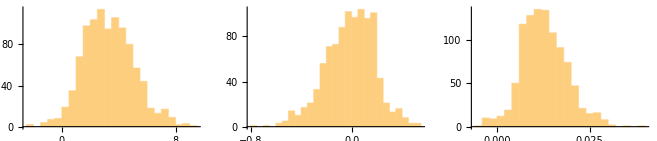

```mathematica
p=GraphicsRow[GetStanResult[Histogram[#,ImageSize->200]&,stanResult,"beta"]]
```

```mathematica
Export["~/GitHub/MathematicaStan/figures/linReg2Histo.png",p]
```

~/GitHub/MathematicaStan/figures/linReg2Histo.png

Run Stan: “method=Sample”

```mathematica
stanResultFile=RunStan[stanExeFile,OptimizeDefaultOptions]
```

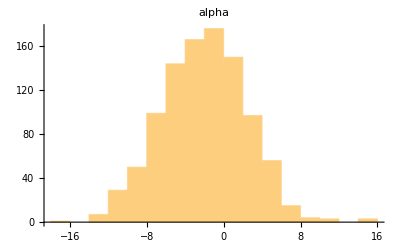
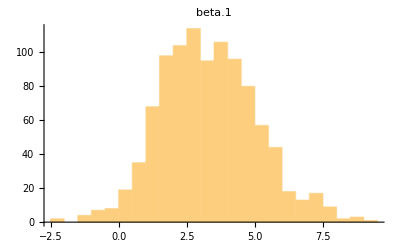
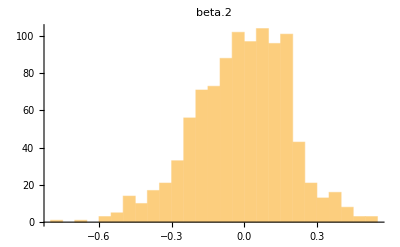
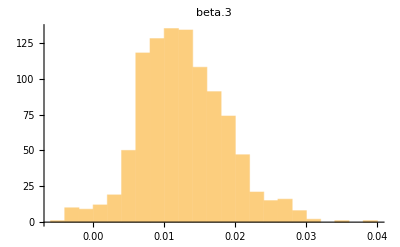
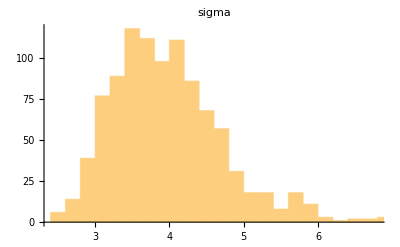

```mathematica
e=Map[#->GetStanResult[stanResult,#]&,StanResultKeys[stanResult]];
Map[Histogram[Values[#],PlotLabel->Keys[#]]&,e]
```

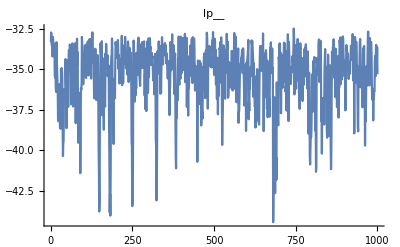
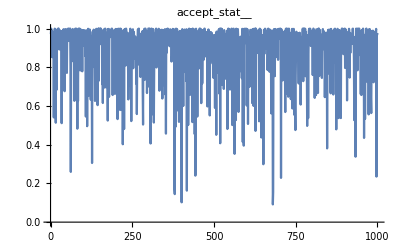
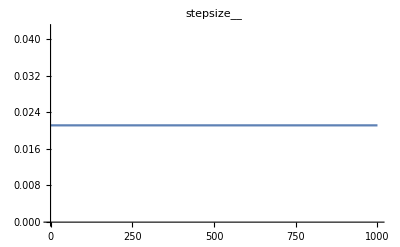
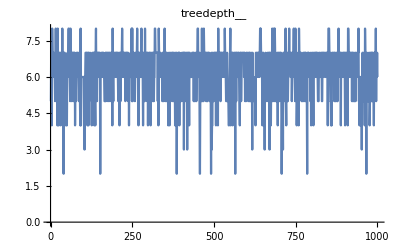
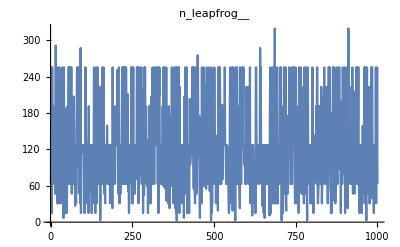
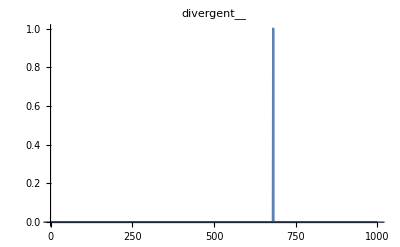
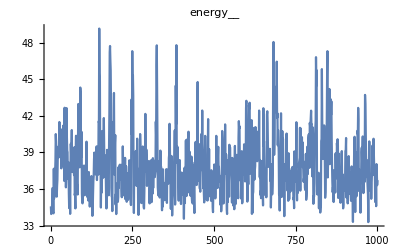

```mathematica
e=Map[#->GetStanResultMeta[stanResult,#]&,StanResultMetaKeys[stanResult]];
Map[ListLinePlot[Values[#],PlotLabel->Keys[#]]&,e]
```

```mathematica
Map[Histogram[Values[#],PlotLabel->Keys[#]]&,e]
```

Histogram::ldata: GetStanResult[     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ,     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ] is not a valid dataset or list of datasets.

GetStanResultKeys[Histogram[GetStanResult[     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ,     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ],PlotLabel→     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ]]

```mathematica
MapStanResult[Mean,myResult,"alpha"]
MapStanResult[Variance,myResult,"alpha"]
MapStanResult[Histogram,myResult,GetStanResultKeys[myResult]]
```

MapStanResult[Mean,     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ,alpha]

MapStanResult[Variance,     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ,alpha]

MapStanResult[Histogram,     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ,GetStanResultKeys[     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ]]

```mathematica
myResult
```

file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma

```mathematica
Export["~/GitHub/MathematicaStan/figures/linRegHisto.png",%]
```

~/GitHub/MathematicaStan/figures/linRegHisto.png

```mathematica
E
```

ⅇ

```mathematica
MapStanResult[Histogram,myResult,"beta"]
```

MapStanResult[Histogram,     file: /tmp/myOutputFile.csv
     meta: lp__ , log_p__ , log_g__ 
parameter: alpha , beta , sigma ,beta]

```mathematica
?MapStanResult
```

Global`MapStanResult